```mathematica
n=1000; m=1000;
```

```mathematica
kaux={}; x=0; lgct={}; lmct={}; llcct={}; lgcr={}; lmcr={}; llccr={};Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n],llcct=Join[llcct, LocalClusteringCoefficient[Graph[t]]],llccr=Join[llcct, LocalClusteringCoefficient[Graph[r]]],cc=ConnectedComponents[Graph[t]],  x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]],Do[{ llcct=Join[llcct, {0}], llccr=Join[llccr, {0}]}, x],  lgct=Join[lgct, {GlobalClusteringCoefficient[Graph[t]]}], lmct=Join[lmct, {MeanClusteringCoefficient[Graph[t]]}], lgcr=Join[lgcr, {GlobalClusteringCoefficient[Graph[r]]}], lmcr=Join[lmcr, {MeanClusteringCoefficient[Graph[r]]}]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Print[N[Mean[lgct]]]; Print[StandardDeviation[N[lgct]]]; Print[N[Mean[lmct]]]; Print[N[StandardDeviation[lmct]]];
```

0.00104502

0.0017439

0.00104377

0.00174177

```mathematica
Print[N[Mean[lgcr]]]; Print[StandardDeviation[N[lgcr]]]; Print[N[Mean[lmcr]]]; Print[N[StandardDeviation[lmcr]]];
```

0.00100079

0.00172237

0.000998808

0.00171902

```mathematica
w=(Max[llcct]-Min[llcct])/Sqrt[Length[llcct]]; bllcc=HistogramList[llcct, {Min[llcct], Max[llcct], w}]; hllcc=Table[{bllcc[[1, i]], bllcc[[2, i]]/(Length[llcct]*w)}, {i, 1, Length[bllcc[[2]]]}];TableForm[N[hllcc]]
```

```mathematica
w=(Max[llccr]-Min[llccr])/Sqrt[Length[llccr]]; bllcc=HistogramList[llccr, {Min[llccr], Max[llccr], w}]; hllcc=Table[{bllcc[[1, i]], bllcc[[2, i]]/(Length[llccr]*w)}, {i, 1, Length[bllcc[[2]]]}];TableForm[N[hllcc]]
```

```mathematica
GraphAssortativity[Graph[t]]
```

48563/111283

```mathematica
kaux={}; x=0; lat={}; lar={}; Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_001.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_001.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n], lat=Join[lat, {GraphAssortativity[Graph[t]]}], lar=Join[lar, {GraphAssortativity[Graph[r]]}]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Print[Mean[N[lat]]]; Print[StandardDeviation[N[lat]]]; Print[Mean[N[lar]]];Print[StandardDeviation[N[lar]]];
```

0.419455

0.0662457

0.062608

0.0408529

```mathematica
n=20; m=1;
```

```mathematica
kaux={}; x=0; lat={}; lar={}; Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Test01.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Test01.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n]},m];
```

```mathematica
Matr=GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]];
```

```mathematica
MatrixForm[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]]
```

(0 | 1 | 3 | 4 | 2 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 6 | 5 | 4 | 4 | 1 | 6 | 5 | 4
0 | 0 | 2 | 3 | 1 | 2 | 1 | 2 | 4 | 4 | 4 | 3 | 7 | 6 | 5 | 5 | 2 | 7 | 6 | 5
0 | 0 | 0 | 1 | 1 | 2 | 3 | 3 | 6 | 6 | 6 | 5 | 9 | 8 | 7 | 7 | 4 | 9 | 8 | 7
0 | 0 | 0 | 0 | 2 | 1 | 2 | 2 | 7 | 7 | 7 | 6 | 10 | 9 | 8 | 8 | 5 | 10 | 9 | 8
0 | 0 | 0 | 0 | 0 | 3 | 2 | 3 | 5 | 5 | 5 | 4 | 8 | 7 | 6 | 6 | 3 | 8 | 7 | 6
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 6 | 6 | 6 | 5 | 9 | 8 | 7 | 7 | 4 | 9 | 8 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5 | 5 | 5 | 4 | 8 | 7 | 6 | 6 | 3 | 8 | 7 | 6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 6 | 6 | 5 | 9 | 8 | 7 | 7 | 4 | 9 | 8 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 3 | 2 | 2 | 1 | 2 | 3 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 3 | 2 | 1 | 1 | 2 | 3 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 3 | 2 | 2 | 2 | 4 | 3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 3 | 2 | 2 | 1 | 4 | 3 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 5 | 4 | 3 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 4 | 3 | 2 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 2 | 1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 2 | 1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | 4 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]], 0];
```

{1,3,4,2,3,2,3,3,3,3,2,6,5,4,4,1,6,5,4,2,3,1,2,1,2,4,4,4,3,7,6,5,5,2,7,6,5,1,1,2,3,3,6,6,6,5,9,8,7,7,4,9,8,7,2,1,2,2,7,7,7,6,10,9,8,8,5,10,9,8,3,2,3,5,5,5,4,8,7,6,6,3,8,7,6,1,1,6,6,6,5,9,8,7,7,4,9,8,7,1,5,5,5,4,8,7,6,6,3,8,7,6,6,6,6,5,9,8,7,7,4,9,8,7,1,1,1,3,2,2,1,2,3,2,2,1,1,3,2,1,1,2,3,2,2,1,4,3,2,2,2,4,3,1,4,3,2,2,1,4,3,2,1,2,2,5,4,3,5,1,1,4,3,2,4,1,3,2,1,3,3,2,1,3,5,4,3,1,5,4}

```mathematica
Do[Print[Count[f, i]], {i, 0, n}];
```

```mathematica
distt=ConstantArray[0, n];Print[distt]; distt+1; Do[{distt[[i]]=distt[[i]]+2*Count[f, i]}, {i, 1, n}]; Print[distt]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{56,64,58,42,38,40,36,26,16,4,0,0,0,0,0,0,0,0,0,0}

```mathematica
T=Total[distt]; M=N[Sum[{i*distt[[i]]}, {i, 1, n}]/T]
```

{4.21053}

```mathematica
SD=N[Sqrt[Sum[distt[[i]]*(i-M)^2, {i, 1, n}]/T]]
```

{2.45119}

```mathematica
Print[N[Mean[f]]]; Print[N[StandardDeviation[f]]]
```

4.21053

2.45766

```mathematica
n=2000; m=1000;
```

```mathematica
kaux={}; x=0; distt=ConstantArray[0,1000]; distr=ConstantArray[0, 1000]; diamt={}; diamr={}; Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Ndep\\Rho000\\NetN2000.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Ndep\\Rho000\\NetN2000.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],r=t,  Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n],f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[t, First[ConnectedComponents[t]]]]]], 0], Do[{distt[[i]]=distt[[i]]+2*Count[f, i]}, {i, 1, 100}], diamt=Join[diamt, {Max[f]}], f=DeleteCases[Flatten[UpperTriangularize[GraphDistanceMatrix[Subgraph[r, First[ConnectedComponents[r]]]]]], 0], Do[{distr[[i]]=distr[[i]]+2*Count[f, i]}, {i, 1, 100}], diamr=Join[diamr, {Max[f]}]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
T=Total[distt]; M=N[Sum[{i*distt[[i]]}, {i, 1, Length[distt]}]/T];Print[M];SD=N[Sqrt[Sum[distt[[i]]*(i-M)^2, {i, 1, Length[distt]}]/(T-1)]]; Print[SD];
```

{50.5}

{28.8661}

```mathematica
T=Total[distr]; M=N[Sum[{i*distr[[i]]}, {i, 1, Length[distt]}]/T];Print[M];SD=N[Sqrt[Sum[distr[[i]]*(i-M)^2, {i, 1, Length[distt]}]/(T-1)]]; Print[SD];
```

{50.4197}

{28.866}

```mathematica
Print[N[Mean[diamt]]];Print[N[StandardDeviation[diamt]]];Print[N[Mean[diamr]]];Print[N[StandardDeviation[diamr]]];
```

631.628

196.235

719.536

329.746

```mathematica
Total[distt]
```

2871330

```mathematica
TableForm[distt]
```

```mathematica
TableForm[distr]
```

```mathematica
TableForm[diamt]
```

```mathematica
TableForm[diamr]
```

```mathematica
n=100; m=1;
```

```mathematica
Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\N100R100.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\N100R100.txt"]]]}], Print["Se leyo la red"],t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}],Print["Se armo t"], r=t,  Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n],Print["Se genero r"]},m];
```

Se leyo la red

Se armo t

Se genero r

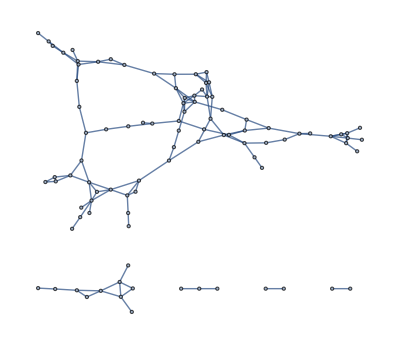

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
Graph[t]
```

```mathematica
Graph[r]
```

-Graphics-

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
n=1000; m=1000;
```

```mathematica
kaux={}; x=0; lgct={}; lmct={}; llcct={}; lgcr={}; lmcr={}; llccr={};Do[{kaux={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_015.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], r=t, Do[{r1=RandomInteger[{1,Length[t] }], r2=RandomInteger[{1,Length[t] }], help=r[[r1, 2]], r[[r1, 2]]=r[[r2,2]], r[[r2, 2]]=help},n],llccr=Join[llccr, LocalClusteringCoefficient[Graph[r]]],cc=ConnectedComponents[Graph[t]],  x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]],Do[{ llccr=Join[llccr, {0}]}, x]},m];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
w=(Max[llccr]-Min[llccr])/Sqrt[Length[llccr]]; bllcc=HistogramList[llccr, {Min[llccr], Max[llccr], w}]; hllcc=Table[{bllcc[[1, i]], bllcc[[2, i]]/(Length[llccr])}, {i, 1, Length[bllcc[[2]]]}];TableForm[N[hllcc]]
```